# Correction Procedure via Reconstruction (CPR)

## CPR: Flux Reconstruction (FR) / Lifting Collocation Penalty (LCP)

## Coded by Manuel Diaz, NTU, 2013.08.20

Based on Ideas of jounal papers:

1. Z.J. Wang & Hai-Yang Gao, JCP 228 (2009) 8161-8186. -> (LCP)
2. H.T. Huynh, AIAA (2007) 4079.->  (FR)
3. Jie Du, Chi-Wang Shu, MengPing Zhang, Brown University (2013) 15.  -> (CPR)

Derivation of the Method in one-dimensional space.

```mathematica
Quit[]; (* to reset Mathematica kernel *)
```

## Initialize Symbols & Notation

#### Change Notebook BackGround

Cool colors:

```mathematica
SetOptions[EvaluationNotebook[],Background->RGBColor[0.1,0.1,0.1]]
```

```mathematica
SetOptions[EvaluationNotebook[],FontColor->RGBColor[170/255,240/255,140/255]]
```

Default colors:

```mathematica
SetOptions[EvaluationNotebook[],Background->RGBColor[1,1,1]]
```

```mathematica
SetOptions[EvaluationNotebook[],FontColor->RGBColor[0,0,0]]
```

#### Adding Notation

```mathematica
Needs["Notation`"]
```

```mathematica
(* Derivatives *)
```

```mathematica
Notation[(∂f_[x_])/(∂x_) ⟸ Derivative[1][f_][x_]]
Notation[(∂^n_ f_[x_])/(∂x_^n_) ⟸ Derivative[n_][f_][x_]]
Notation[(∂f_[x_,y_])/(∂x_) ⟸ Derivative[{1,0}][f_][{x_,y_}]]
Notation[(∂f_[x_,y_])/(∂y_) ⟸ Derivative[{0,1}][f_][{x_,y_}]]
Notation[(∂f_[x_,y_,z_])/(∂x_) ⟸ Derivative[{1,0,0}][f_][{x_,y_,z_}]]
Notation[(∂f_[x_,y_,z_])/(∂y_) ⟸ Derivative[{0,1,0}][f_][{x_,y_,z_}]]
Notation[(∂f_[x_,y_,z_])/(∂z_) ⟸ Derivative[{0,0,1}][f_][{x_,y_,z_}]]
Notation[(∂f_[x_,y_,z_,t_])/(∂x_) ⟸ Derivative[{1,0,0,0}][f_][{x_,y_,z_,t_}]]
Notation[(∂f_[x_,y_,z_,t_])/(∂y_) ⟸ Derivative[{0,1,0,0}][f_][{x_,y_,z_,t_}]]
Notation[(∂f_[x_,y_,z_,t_])/(∂z_) ⟸ Derivative[{0,0,1,0}][f_][{x_,y_,z_,t_}]]
Notation[(∂f_[x_,y_,z_,t_])/(∂t_) ⟸ Derivative[{0,0,0,1}][f_][{x_,y_,z_,t_}]]
```

```mathematica
(* Divergence *)
```

```mathematica
Notation[∇_x_ ·f_ ⟹ Div[{f_[{x_,t}]},{x_}]]
Notation[∇_(x_,y_) ·{f_,g_} ⟹ Div[{f_[{x_,y_,t}],g_[{x_,y_,t}]},{x_,y_}]]
Notation[∇_(x_,y_,z_) ·{f_,g_,h_} ⟹ Div[{f_[{x_,y_,z_,t}],g_[{x_,y_,z_,t}],h_[{x_,y_,z_,t}]},{x_,y_,z_}]]
```

```mathematica
(* For Gauss Rule *)
```

```mathematica
Notation[∫∂_x_ (a_[{x_,t}]b_[x_])ⅆx_ ⟹ a_^(\[MathematicaIcon])[{Subscript[x_, k+1/2],t}] b_[Subscript[x_, k+1/2]] - a_^(\[MathematicaIcon])[{Subscript[x_, k-1/2],t}] b_[Subscript[x_, k-1/2]]]
```

```mathematica
Symbolize[Subscript[f̂, j-1/2]];
```

```mathematica
Symbolize[Subscript[f̂, j+1/2]];
```

```mathematica
Notation[<a_,b_> ⟹ Integrate[a_ b_,{ξ,-1,1}]];
(* Notation[<<a_,b_>> ⟹ Integrate[a_ b_,{ξ,-1,1}],{}]; *)
```

## Lifting Collocation Penalty Formulation for T3

### Initial Data

T3= { (r,s) | r,s ≥ 0 , r+s ≤ 1}

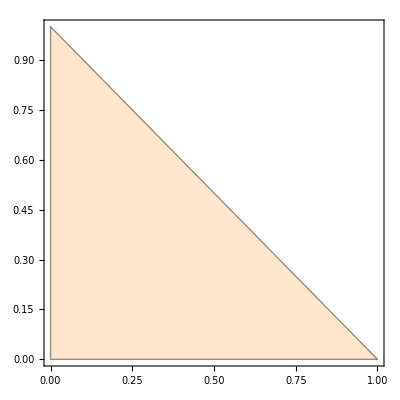

```mathematica
ClearAll[Simplex2D]
Simplex2D = RegionPlot[r≥0 && s≥ 0 && s+r≤1,{r,0,1},{s,0,1},PlotStyle->LightOrange]
```

### T3 Nodes

assume coordinates for the triangle / also they are our solution points:

```mathematica
({{Subscript[x, 1], Subscript[y, 1]}, {Subscript[x, 2], Subscript[y, 2]}, {Subscript[x, 3], Subscript[y, 3]}})=({{0, 0}, {1, 0}, {0, 1}});
```

```mathematica
nodesT3 = {{Subscript[x, 1],Subscript[y, 1]},{Subscript[x, 2],Subscript[y, 2]},{Subscript[x, 3],Subscript[y, 3]}}
```

{{0,0},{1,0},{0,1}}

```mathematica
nodesT3plot=ListPlot[nodesT3,PlotStyle->PointSize[Large]];
```

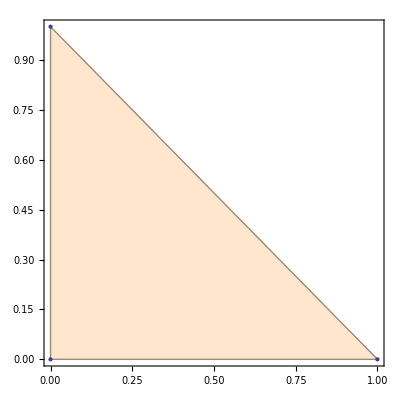

```mathematica
Show[Simplex2D,nodesT3plot]
```

### Nodes Fluxes

Each flux is normal to its face

Face 1: nodes 1-2

```mathematica
Subscript[F, 1,1];
Subscript[F, 1,2];
```

Face 2:  nodes 2-3

```mathematica
Subscript[F, 2,1];
Subscript[F, 2,2];
```

Face 3: nodes 3-1

```mathematica
Subscript[F, 3,1];
Subscript[F, 3,2];
```

### L2 Element Shape Function

Based on Lagrange Interpolations for a local projection

```mathematica
{Subscript[ξ, 1],Subscript[ξ, 2]} = {0,1};
```

```mathematica
StencilPoints[r_] := Table[{Subscript[ξ, i],Subscript[q, i]},{i,1,r}]
```

```mathematica
LagrangePolynomial[data_,x_]/;MatrixQ[data]:=
Module[{n=Length[data], xl,yl},
{xl,yl}=Transpose[data];
Table[Product[(x-xl[[i]])/(xl[[j]]-xl[[i]]),{i,Complement[Range[n],{j}]}],{j,n}]
]
```

```mathematica
{N1,N2}=LagrangePolynomial[StencilPoints[2],ξ]//Expand// Simplify
```

{1-ξ,ξ}

```mathematica
{M1,M2}=LagrangePolynomial[StencilPoints[2],η]//Expand// Simplify
```

{1-η,η}

shape functions face 1

```mathematica
{Subscript[ϕ, 1],Subscript[ϕ, 2]}={N1,N2}/.ξ->x
```

{1-x,x}

shape functions face 2

```mathematica
{Subscript[χ, 1],Subscript[χ, 2]}={N2,N1}{M1,M2}/.ξ -> x/.η->y
```

{x (1-y),(1-x) y}

shape functions face 3

```mathematica
{Subscript[ψ, 1],Subscript[ψ, 2]}={M1,M2}/.η->y
```

{1-y,y}

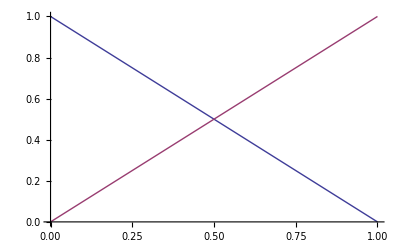

-Graphics3D-

-Graphics-

```mathematica
Plot[{Subscript[ϕ, 1],Subscript[ϕ, 2]},{x,0,1}]
Plot3D[{Subscript[χ, 1],Subscript[χ, 2]},{x,0,1},{y,0,1-x}]
Plot[{Subscript[ψ, 1],Subscript[ψ, 2]},{y,0,1}]
```

### T3 Element Shape Function

Based on linear polynomial, u^e(x_) = α_0^e+α_1^e x

```mathematica
coef = ({{Subscript[α, 0]}, {Subscript[α, 1]}, {Subscript[α, 2]}});
p[x_,y_]:= ({{1, x, y}})
M= ({{1, Subscript[x, 1], Subscript[y, 1]}, {1, Subscript[x, 2], Subscript[y, 2]}, {1, Subscript[x, 3], Subscript[y, 3]}});
```

```mathematica
u=  p[x,y].coef
```

{{α_0+x α_1+y α_2}}

```mathematica
Area=1/2Det[M]//Simplify
```

1/2

```mathematica
Inverse[M]2*Area //Simplify
```

{{1,0,0},{-1,1,0},{-1,0,1}}

```mathematica
Ne[x_,y_]:= p[x,y].Inverse[M]
```

```mathematica
Ne[x,y] //Simplify
```

{{1-x-y,x,y}}

```mathematica
{Subscript[ℒ, 1],Subscript[ℒ, 2],Subscript[ℒ, 3]}=Flatten[Ne[x,y]//Simplify];
```

```mathematica
Table[Plot3D[Subscript[ℒ, i],{x,0,1},{y,0,1-x}],{i,1,3}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

test:

```mathematica
Subscript[ℒ, 1]
```

1-x-y

### LCP

Introduce the correction field

∫_v_i W δ_iⅆV = ∫_(∂V_i) W [OverTilde[F]]ⅆS

where 
OverTilde[[F]] = F̃(Q^h, (Q_+)^h,n⃗)-F^n(Q_i^h)

doing w = 1 LCP correction term yields,

∫_V_i δ_i ⅆV == ∫_(∂V_i) [F̃] ⅆS

or

OverBar[δ_i]= 1/(|V_i|)∑_(f∈∂V_i) ∫_f [F̃]ⅆS

using a suitable on the face of every element yields,

OverBar[δ_i]= 1/(|V_i|)∑_(f∈∂V_i) ∑_l w_l[F̃]_(f,l)S_f

According to Eq. 3.13, the penalty correction at the solution points are computed using,

δ_(i,j)=1/(|v_i|)∑_(f∈∂V_i) ∑α_(j,f,l)OverTilde[[F]]_(f,l)S_f

here |v_i| is the volume of cell i, (F̃)_(f,l) is the flux difference computed at the lth flux point along face f, and S_f is simply the area of f.

### LCP - LHS term:

```mathematica
prod = Table[Subscript[ℒ, k] Sum[Subscript[δ, i,j] Subscript[ℒ, j],{j,1,3}],{k,1,3}] //Simplify;
prod //TableForm
```

(1-x-y) (-(-1+x+y) δ_(i,1)+x δ_(i,2)+y δ_(i,3))
x (-(-1+x+y) δ_(i,1)+x δ_(i,2)+y δ_(i,3))
y (-(-1+x+y) δ_(i,1)+x δ_(i,2)+y δ_(i,3))

```mathematica
prod = Table[Subscript[ℒ, k] Subscript[ℒ, j],{k,1,3},{j,1,3}];
prod //TableForm
```

(1-x-y)^2 | x (1-x-y) | (1-x-y) y
x (1-x-y) | x^2 | x y
(1-x-y) y | x y | y^2

example: integrate constant 1 over the interize domain of T3:

```mathematica
Integrate[1,{x,0,1},{y,0,1-x}]
```

1/2

```mathematica
massMatrix = Integrate[Evaluate[prod],{x,0,1},{y,0,1-x}];
massMatrix //MatrixForm
```

(1/12 | 1/24 | 1/24
1/24 | 1/12 | 1/24
1/24 | 1/24 | 1/12)

```mathematica
invMassMatrix = Inverse[massMatrix];
invMassMatrix //MatrixForm
```

(18 | -6 | -6
-6 | 18 | -6
-6 | -6 | 18)

### LCP - RHS term:

for the RHs,

For Face 1

```mathematica
prod2 = Table[Subscript[ℒ, k] Sum[Subscript[F, f,l] Subscript[ϕ, l],{l,1,2}],{k,1,3}] /.y ->0//Simplify;
prod2//MatrixForm
```

((1-x) (-(-1+x) F_(f,1)+x F_(f,2))
x (-(-1+x) F_(f,1)+x F_(f,2))
0)

```mathematica
prod3 = Table[Subscript[ℒ, k] Sum[Subscript[F, f,l] Subscript[χ, l],{l,1,2}],{k,1,3}] //Simplify;
prod3 // MatrixForm
```

((1-x-y) ((x-x y) F_(f,1)-(-1+x) y F_(f,2))
x ((x-x y) F_(f,1)-(-1+x) y F_(f,2))
y ((x-x y) F_(f,1)-(-1+x) y F_(f,2)))

```mathematica
prod4 = Table[Subscript[ℒ, k] Sum[Subscript[F, f,l] Subscript[ψ, l],{l,1,2}],{k,1,3}] /.x ->0//Simplify;
prod4 // MatrixForm
```

((1-y) (-(-1+y) F_(f,1)+y F_(f,2))
0
y (-(-1+y) F_(f,1)+y F_(f,2)))

#### Build matrix coeficients

```mathematica
prod2 = Table[Subscript[ℒ, k] Table[Subscript[ϕ, l],{l,1,2}],{k,1,3}];
prod2 //MatrixForm
```

((1-x) (1-x-y) | x (1-x-y)
(1-x) x | x^2
(1-x) y | x y)

```mathematica
rhsMatrix1 = Integrate[Evaluate[prod2],{x,0,1}]/.y->0;
rhsMatrix1 //MatrixForm
```

(1/3 | 1/6
1/6 | 1/3
0 | 0)

```mathematica
prod3 = Table[Subscript[ℒ, k] Table[Subscript[χ, l],{l,1,2}],{k,1,3}];
prod3 //MatrixForm
```

(x (1-y) (1-x-y) | (1-x) (1-x-y) y
x^2 (1-y) | (1-x) x y
x (1-y) y | (1-x) y^2)

```mathematica
rhsMatrix2 = Integrate[Evaluate[prod3],{x,0,1},{y,0,1}];
rhsMatrix2  //MatrixForm
```

(0 | 0
1/6 | 1/12
1/12 | 1/6)

```mathematica
prod4 = Table[Subscript[ℒ, k] Table[Subscript[ψ, l],{l,1,2}],{k,1,3}]/.x ->0;
prod4//MatrixForm
```

((1-y)^2 | (1-y) y
0 | 0
(1-y) y | y^2)

```mathematica
rhsMatrix3 = Integrate[Evaluate[prod4],{y,0,1}];
rhsMatrix3 //MatrixForm
```

(1/3 | 1/6
0 | 0
1/6 | 1/3)

### Lift Coeficients α_(j,f,l)

```mathematica
invMassMatrix.rhsMatrix1 //N// MatrixForm
invMassMatrix.rhsMatrix2 //N// MatrixForm
invMassMatrix.rhsMatrix3 //N// MatrixForm
```

(5. | 1.
1. | 5.
-3. | -3.)

(-1.5 | -1.5
2.5 | 0.5
0.5 | 2.5)

(5. | 1.
-3. | -3.
1. | 5.)